```mathematica
Clear[p]
```

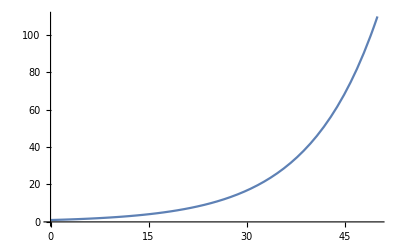
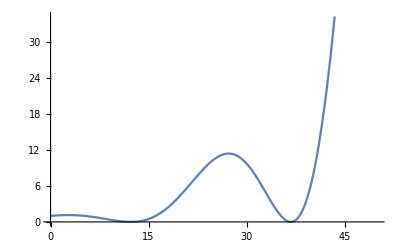
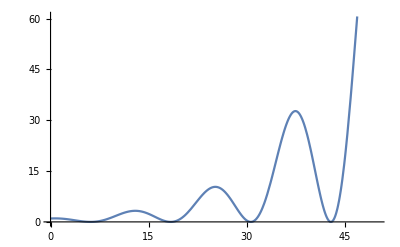
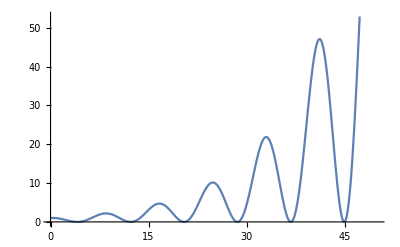
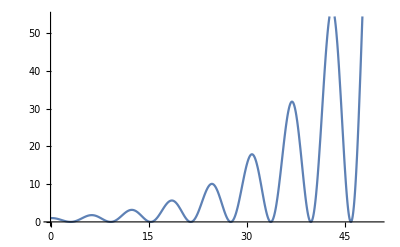
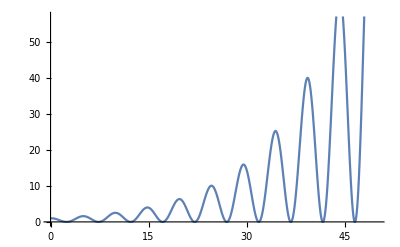
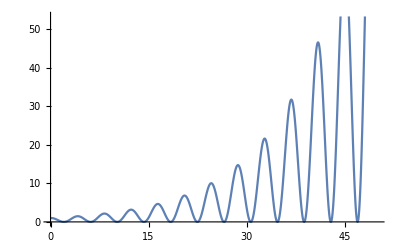
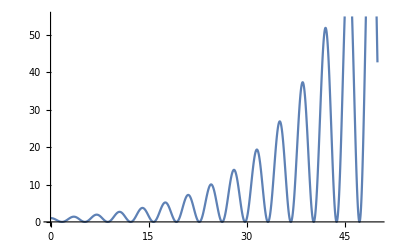

```mathematica
c=1;
m=100;
n=50;
a=(2 p π)/(n-1);
b=Log[m/(c Cos[a (n-1)]^2)]/(n-1);
f[x_]:=c Cos[a x]^2 Exp[b x]
Table[Plot[f[x],{x,0,50}],{p,0,9}]
```

```mathematica
Table[f[49],{p,0,9}]
```

{100,100,100,100,100,100,100,100,100,100}